```mathematica
SetDirectory[NotebookDirectory[]];
sawSpecDictLL=Import["N-Specs/sawSpecsLL.m"];
boxSpecDictLL=Import["N-Specs/boxSpecsLL.m"];
sawSpecDictGG=Import["N-Specs/sawSpecsGG.m"];
boxSpecDictGG=Import["N-Specs/boxSpecsGG.m"];
```

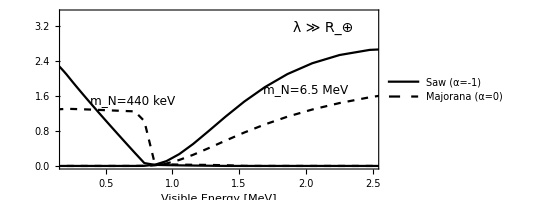

```mathematica
LLplt1=ListPlot[{({#⟦1⟧,0.1#⟦2⟧}&)/@ sawSpecDictGG[(Keys@sawSpecDictGG)⟦18⟧],({#⟦1⟧,0.1#⟦2⟧}&)/@ boxSpecDictGG[(Keys@sawSpecDictGG)⟦18⟧],({#⟦1⟧,20000 #⟦2⟧}&)/@ sawSpecDictGG[(Keys@sawSpecDictGG)⟦30⟧],({#⟦1⟧,20000 #⟦2⟧}&)/@ boxSpecDictGG[(Keys@sawSpecDictGG)⟦30⟧]},Joined->True,PlotRange->{{0.2,2.5},{0,3.5}},PlotLegends->Placed[{"Saw (α=-1)","Majorana (α=0)"},{0.45,0.85}],PlotStyle->{Black,{Black,Dashed}},Frame->True  ,FrameStyle->Black,Epilog->{Inset[Style["m_N=440 keV",12],{0.7,1.5}],Inset[Style["m_N=6.5 MeV",12],{2,1.75}],Inset[Style["λ ≫ R_⊕",14],{2.13,3.15}]},FrameLabel->(Style[#,12]&)/@{"Visible Energy    [MeV]"},AspectRatio->1/2]
```

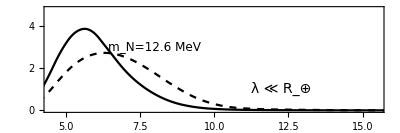

```mathematica
LLplt2=ListPlot[{({#⟦1⟧,8000000#⟦2⟧}&)/@ sawSpecDictLL[(Keys@sawSpecDictGG)⟦33⟧],({#⟦1⟧,8000000#⟦2⟧}&)/@ boxSpecDictLL[(Keys@sawSpecDictGG)⟦33⟧]},Joined->True,InterpolationOrder->2,PlotRange->{{4.49,15.5},{0,4.8}},PlotLegends->Placed[ {"Saw (α=-1)","Majorana (α=0)"},{0.75,0.75}],PlotStyle->{Black,{Black,Dashed}},Frame->True  ,FrameStyle->Black,FrameLabel->(Style[#,12]&)/@{"Visible Energy    [MeV]"},Epilog->{Inset[Style["m_N=12.6 MeV",12],{8,3}],Inset[Style["λ ≪ R_⊕",14],{12.25,1}]},PlotRangePadding->{0,0},AspectRatio->1/3]
```

```mathematica
Export["PDFs/MvsD1.pdf",LLplt1];
Export["PDFs/MvsD2.pdf",LLplt2];
```